Quantum States for 1-Electron Systems Using NDEigensystem

Arango Carlos

Abbott Paul

Department of Chemical Sciences, Universidad Icesi, Cali - Colombia

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Develop an interactive notebook to be used in quantum chemistry undergraduate courses.

SUMMARY OF WORK: Although the hydrogen atom and molecule ion are the simplest cases to study in Quantum Chemistry, finding their analytical solutions is not trivial, even in 1 dimension. This notebook allows Chemistry major students to solve Schrödinger’s equation numerically and obtain eigenvalues and eigenvectors for 1-electron systems. For the systems of interest, H and H_2^+, electronic states are calculated numerically using NDEigensystem. The electronic wave functions are visualized as functions of numerical parameters and physical constrains by using the interactive interface of Manipulate.

RESULTS AND FUTURE  WORK: Through this notebook students can calculate electronic states of H and H_2^+ by varying numerical and physical parameters such as the discretization interval or the bond length. The exercises and investigations allow students to explore the validity of numerical solutions. For H_2^+ in 1-dimension the student is guided to the calculation of nuclear energy curves within the Born-Oppenheimer approximation. The definitions of the Hamiltonian and functions—based on NDEigensystem—allow an easy and systematic extension to larger systems in 3 dimensions, or with 2 electrons.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

## 1 and 2 Dimensions Hydrogen atom

```mathematica
-Graphics--Graphics-
```

## 1 and 2 Dimensions Hydrogen Molecule Ion

```mathematica
-Graphics--Graphics-
```

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Definition of a generalized Hamiltonian functions for the 1-electron Coulomb problem with one or two protons.

Interactive Manipulate window (box) showing the lowest energy wavefunctions of NDEigensystem for the 1-electron systems H and H_2^+ in 1 and 2 dimensions. This graphical interface allows to explore the reach and limitation of the numerical solutions by comparing with analytical eigenfunctions and eigenvalues.

Born-Oppenheimer nuclear curves for 1-dimension H_2^+.

Code

Link to the GitHub: https://github.com/caarango/WSS_project/blob/master/QS1e.nb

Written Content / Lesson Plans

Quantum Chemistry/Mathematica, QC/M, is a course planned to teach the foundations and applications of quantum mechanics in chemistry by using Wolfram Language. The first third of QC/M will give an introduction to classical and quantum mechanics, the second part of the course introduces the application of quantum mechanics to atoms and molecules. The final third will deal with modern applications like quantum dynamics in chemistry and molecular spectroscopy. Although this seems an ambitious course for a third year undergraduate chemistry major, this course will relies upon the student’s background in Mathematics, Physics and the use of Wolfram Language to compute wave functions. 

This notebook will cover the introduction to atomic and molecular orbitals by using Mathematica to compute the electronic wave function for Hydrogen and Hydrogen molecule ion. Students will have the opportunity to learn by inquiring into the notebook content and instructions. They could learn about the relation between the solutions of Schrödinger’s equation and the physical constrains imposed on molecular systems. The content of this notebook is:

Hamiltonian Operator for the Coulomb potential: central force

The 1-dimension Hydrogen atom

Boundary conditions

Eigensystem

Computing the lowest energy eigenstates

The 2-dimension Hydrogen atom

Boundary conditions and integration region

Eigensystem with annular integration region

Eigensystem with a disklike integration region

The potential energy surface and the ground state

The 1-dimension hydrogen molecule ion: H_2^+

Hamiltonian: regularization of the Coulomb potential

Eigensystem

Born-Oppenheimer curves

The 2-dimension hydrogen molecule ion: H_2^+

Redefining the Hamiltonian: List and Sequence

Eigensystem and lowest energy states

Conclusions in Detail

This notebook will be used in the quantum chemistry course during the fall-2017 semester. The Hydrogen atom and the Hydrogen molecular ion are of fundamental importance to understand the principles of the chemical bonding. The concept of atomic or molecular orbital is not clearly understood for many chemistry undergraduate students, and probably a reason for this is the passive role of students in typical quantum chemistry lectures. The student can use this notebook to make/do real quantum chemistry, in an active way, by computing orbitals of atoms and molecules. The elaboration of this notebook took  approximately two weeks, but there is still some work to be done for the realistic 3-dimension Hydrogen atom and molecule ion. This is enough class material to cover 3 weeks of the 16 weeks academic semester. As a professor and researcher in the field of theoretical and quantum chemistry, I am convinced of the importance for the students of learning to do molecular simulations. Chemistry has moved from studying proportion laws and stoichiometry to the formation and destruction of single chemical bonds. Theoretical tools as computer simulations give a first insight and a direct molecular description of chemical reactions, therefore a computational thinking is of central importance to learn not only quantum chemistry but chemistry in general. It is my expectation that this initiative could be extended to courses of Physics and Mathematics at Universidad Icesi in Cali - Colombia.

All Visualizations

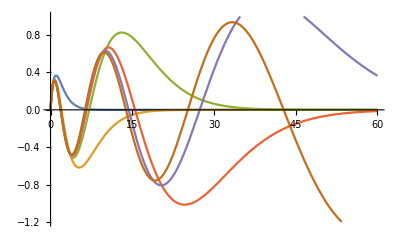
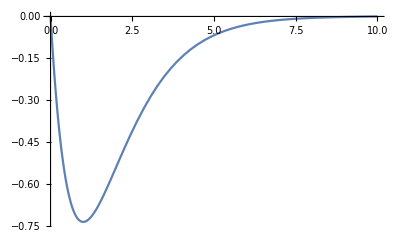
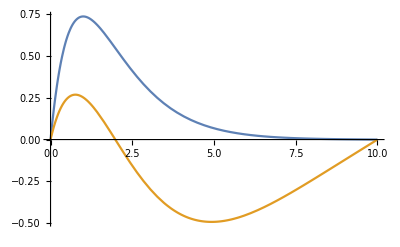
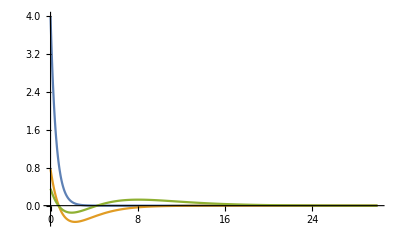
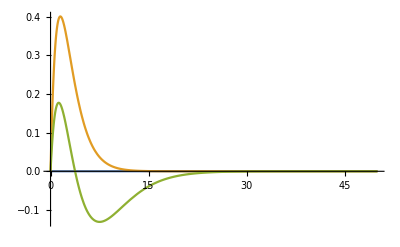
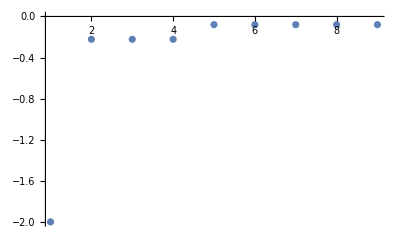
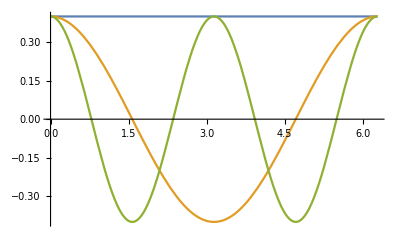
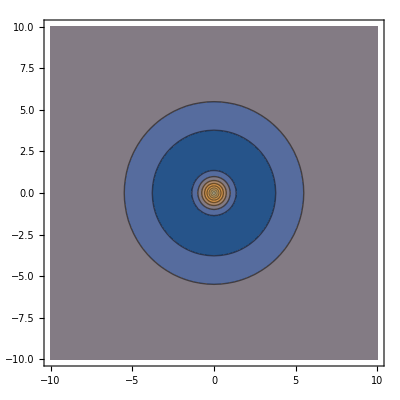

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics3D--Graphics--Graphics3D--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics3D--Graphics3D--Graphics3D--Graphics--Graphics--Graphics3D--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics3D--Graphics3D--Graphics-
```

Data Sources Links/References

Future Directions

The structure of functions and the notebook will allow straightforward extensions to 2 - electron and/or 3 - dimension systems.

The inclusion of a kinetic energy operator for the nuclei will allow to deal with systems with strong nuclear-electronic correlation.

Enrich the content of this notebook with contextualization about the use of quantum mechanics in chemistry.

Solve the 1-dimensional Hydrogen molecule ion with multiple domains connected through boundaries by requiring continuity of the electron wave function and its derivative.

Background Info Links/References

[1] Moss, R. E., “The Hydrogen atom in one dimension”, Am. J. Phys. 55, 397, 1987
[2] Palma, G., Ulrich R., “The one-dimensional hydrogen atom revisited”, Canadian Journal of Physics,  84(9): 787-800, 2006
[3] Loudon, R, “One-dimensional hydrogen atom”, Proc. R. Soc. A, 472 20150534, 2016
[4] Yang, X. L., Guo, S.H., Chan, F. T., Wong, K. W., Ching, W. Y., “Analytical solution of a two-dimensional hydrogen atom. I. Nonrelativistic theory”, 	Phys. Rev. A, 43, 1186, 1991
[5] Hasoun, G. Q., “Two-particle 1-dimensional model of the Hydrogen molecular ion in an ultrashort laser pulse”,  Am. J. Phys. 49 (2), 143, 1981
[6] Duan, Y, Yin, M., An, W., He, C., “A one-dimensional Model of Hydrogen Molecular Ion”, Commun. Theor. Phys. (Beijing, China), 31, 27-32, 1999
[7] Dutta, S. Shreemoyee, G., Dutta-Roy, B., “A cartoon in one dimension of the hydrogen molecular ion”, European Journal of Physics 29, 235, 2008
[8] Patil, S. H. “Hydrogen molecular ion and molecule in two dimensions” J. Chem. Phys. 118, 2197, 2003

Keywords

1-electron Coulomb systems

Born-Oppenheimer approximation

1-dimension hydrogen atom

1-dimension hydrogen molecule ion

2-dimension hydrogen atom

2-dimension hydrogen molecule ion

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```